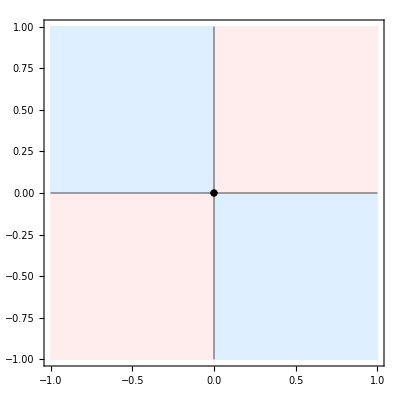

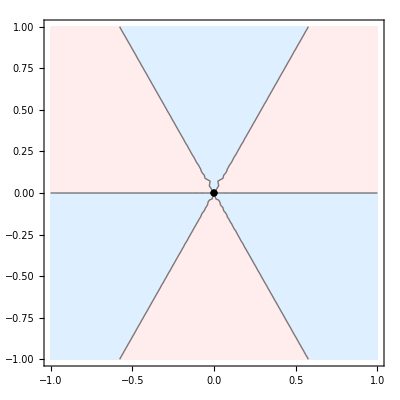

```mathematica
diag=1+I;
proc[f_,a_,b_]:=Module[{cp,lp},
cp=ComplexContourPlot[Im[f],{z,a-b*diag,a+b*diag},
Contours->{0},ContourShading->{LightBlue,LightPink}];
lp=ComplexListPlot[{0},PlotStyle->{Black,size}];
Show[cp,lp]];
pz=proc[z^2,0,1]
pw=proc[z^3,0,1]
```